# SSS and the Tricky Play of Albedo Remapping

## Companion notebook

Max Tarpini · rombo.tools

The article tells the story, this notebook lets you play with it: simulate the curve, drag the remaps, watch the radius and the noise. 
Read the article first: [link to the article].
Evaluation -> Evaluate Notebook. Sections 2 and 5 may take a few seconds.

## 1. Making the curve

A tiny Monte Carlo: shoot light into a semi-infinite slab (isotropic scattering, index-matched boundary, diffuse incidence, distances in mean free paths) and count what comes back. That is A for a given α. Then fit Disney's curve shape on our own data.

```mathematica
SeedRandom[2026];

slabAlbedo = Compile[{{alpha, _Real}, {n, _Integer}},
   Module[{esc = 0, z = 0., mu = 1., alive = True},
    Do[
     z = 0.; mu = Sqrt[RandomReal[]]; alive = True;   (* diffuse (cosine-weighted) entry *)
     While[alive,
      z += -mu Log[RandomReal[]];                  (* free flight, sigma_t = 1 *)
      If[z < 0.,
       esc++; alive = False,                        (* back out through the surface *)
       If[RandomReal[] > alpha,
        alive = False,                              (* absorbed *)
        mu = 2. RandomReal[] - 1.]                  (* isotropic bounce *)
       ]],
     {n}];
    1. esc/n]];
```

```mathematica
alphas = Join[Range[0.05, 0.95, 0.05], {0.97, 0.98, 0.99, 0.995, 0.998}];

AbsoluteTiming[
 data = Table[{slabAlbedo[a, 20000], a}, {a, alphas}];   (* pairs {A, alpha} *)
]
```

{0.566892,Null}

Fit Disney's shape, α = 1 − exp(c1 A + c2 A.b2 + c3 A.b3), on the simulated points:

```mathematica
fit = FindFit[data, 1 - Exp[c1 A + c2 A^2 + c3 A^3], {{c1, -5}, {c2, 2}, {c3, -4}}, A];

Grid[{
  {"", "c1", "c2", "c3"},
  {"our fit", c1 /. fit, c2 /. fit, c3 /. fit},
  {"Disney (Chiang et al. 2016)", -5.09406, 2.61188, -4.31805}},
 Frame -> All, Alignment -> Right]
```

| c1 | c2 | c3
our fit | -4.90803 | 1.76188 | -3.35427
Disney (Chiang et al. 2016) | -5.09406 | 2.61188 | -4.31805

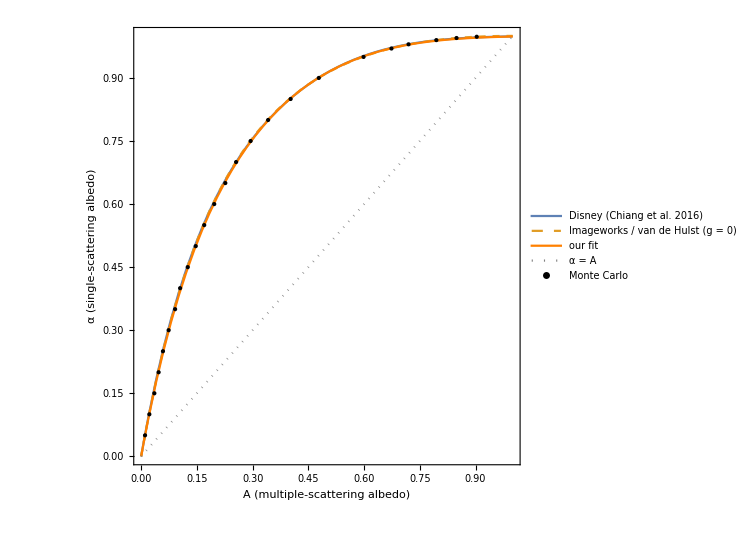

```mathematica
alphaChiang[A_] := 1 - Exp[-5.09406 A + 2.61188 A^2 - 4.31805 A^3];

alphaVdH[A_, g_: 0] := Module[{s = 4.09712 + 4.20863 A - Sqrt[9.59217 + 41.6808 A + 17.7126 A^2]},
   (1 - s^2)/(1 - g s^2)];

Show[
 Plot[{alphaChiang[A], alphaVdH[A], 1 - Exp[c1 A + c2 A^2 + c3 A^3] /. fit, A}, {A, 0, 1},
  PlotStyle -> {Thick, Dashed, Directive[Thick, Orange], Directive[Gray, Dotted]},
  PlotLegends -> {"Disney (Chiang et al. 2016)", "Imageworks / van de Hulst (g = 0)", "our fit", "α = A"}],
 ListPlot[data, PlotStyle -> Directive[Black, PointSize[Medium]], PlotLegends -> {"Monte Carlo"}],
 Frame -> True, PlotRange -> {{0, 1}, {0, 1}}, AspectRatio -> 1, ImageSize -> 550,
 FrameLabel -> {"A  (multiple-scattering albedo)", "α  (single-scattering albedo)"}]
```

The Monte Carlo points land on top of both published curves. The fitted constants still differ a bit from Chiang's: an exp-cubic is forgiving, and quite different constant sets draw nearly the same curve.

### Checks

```mathematica
(* Monte Carlo vs van de Hulst's forward formula (g = 0) *)
AvdH[a_, g_: 0] := Module[{s = Sqrt[(1 - a)/(1 - g a)]}, (1 - 0.139 s) (1 - s)/(1 + 1.17 s)];

TableForm[
 Table[{d[[2]], d[[1]], AvdH[d[[2]]], d[[1]] - AvdH[d[[2]]]}, {d, data[[;; ;; 3]]}],
 TableHeadings -> {None, {"α", "A (Monte Carlo)", "A (van de Hulst)", "Δ"}}]
```

α | A (Monte Carlo) | A (van de Hulst) | Δ
0.05 | 0.0104 | 0.0102272 | 0.000172762
0.2 | 0.047 | 0.0451739 | 0.00182612
0.35 | 0.09135 | 0.0885402 | 0.00280976
0.5 | 0.1469 | 0.144532 | 0.00236806
0.65 | 0.2265 | 0.221494 | 0.0050057
0.8 | 0.3417 | 0.340343 | 0.00135721
0.95 | 0.59865 | 0.596267 | 0.00238339
0.99 | 0.7945 | 0.79453 | -0.000029991

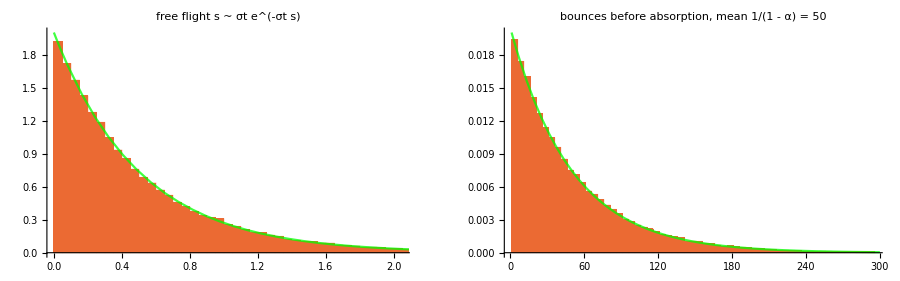

```mathematica
(* Theory vs samples: free flights and bounces before absorption *)
bounceCount = Compile[{{alpha, _Real}, {n, _Integer}},   (* same survival rule as the walk *)
   Table[Module[{k = 1}, While[RandomReal[] <= alpha, k++]; k], {n}]];

With[{sigmaT = 2., alpha = 0.98, n = 10^5},
 GraphicsRow[{
   Show[
    Histogram[-Log[RandomReal[1, n]]/sigmaT, 100, "PDF", PlotTheme -> "WarmColor"],
    Plot[sigmaT Exp[-sigmaT s], {s, 0, 4}, PlotRange -> All,
     PlotStyle -> {Green, Opacity[0.75]}],
    PlotLabel -> "free flight s ~ σt e^(-σt s)"],
   Show[
    Histogram[bounceCount[alpha, n], {1, 300, 5}, "PDF",
     PlotTheme -> "WarmColor"],
    Plot[(1 - alpha) alpha^(k - 1), {k, 1, 300}, PlotRange -> All,
     PlotStyle -> {Green, Opacity[0.75]}],
    PlotLabel -> "bounces before absorption, mean 1/(1 - α) = 50"]},
  ImageSize -> 900]]
```

## 2. The remaps

### Phase function and g

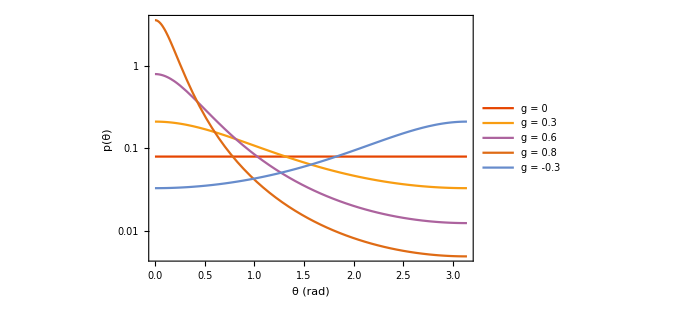

g | ∫ p dω | mean cos
0. | 1. | 0.
0.5 | 1. | 0.5
0.8 | 1. | 0.8

```mathematica
(* Henyey-Greenstein: one parameter, g = mean cosine *)
pHG[g_, ct_] := (1 - g^2)/(4 Pi (1 + g^2 - 2 g ct)^(3/2));

LogPlot[Evaluate[Table[pHG[g, Cos[th]], {g, {0., 0.3, 0.6, 0.8, -0.3}}]], {th, 0, Pi},
 Frame -> True, ImageSize -> 500, PlotTheme -> "WarmColor",
 PlotLegends -> {"g = 0", "g = 0.3", "g = 0.6", "g = 0.8", "g = -0.3"},
 FrameLabel -> {"θ (rad)", "p(θ)"}]

(* normalized, and its mean cosine is g *)
Table[{g, NIntegrate[2 Pi pHG[g, mu], {mu, -1, 1}, AccuracyGoal -> 10],
   NIntegrate[2 Pi mu pHG[g, mu], {mu, -1, 1}, AccuracyGoal -> 10]}, {g, {0., 0.5, 0.8}}]   (* in mu = cos(theta); absolute accuracy, since the g = 0 mean is exactly 0 *) //
 TableForm[#, TableHeadings -> {None, {"g", "∫ p dω", "mean cos"}}] &
```

```mathematica
(* Pixar (Wrenninge, Villemin, Hery 2017): six coefficients, each a degree-7 polynomial in g *)
(* kB, kE: for g < 0 the exponent dives to about -1150, the term is just 0 (fit made for g >= 0); expU flushes it to 0 like expf in C *)
expU[x_] := If[x < -700., 0., Exp[x]];
kA[g_] := 1.8260523782 - 1.28451056436 g - 1.79904629312 g^2 + 9.19393289202 g^3 - 22.8215585862 g^4 + 32.0234874259 g^5 - 23.6264803333 g^6 + 7.21067002658 g^7;
kB[g_] := 4.98511194385 + 0.127355959438 expU[31.1491581433 g - 201.847017512 g^2 + 841.576016723 g^3 - 2018.09288505 g^4 + 2731.71560286 g^5 - 1935.41424244 g^6 + 559.009054474 g^7];
kC[g_] := 1.09686102424 - 0.394704063468 g + 1.05258115941 g^2 - 8.83963712726 g^3 + 28.8643230661 g^4 - 46.8802913581 g^5 + 38.5402837518 g^6 - 12.7181042538 g^7;
kD[g_] := 0.496310210422 + 0.360146581622 g - 2.15139309747 g^2 + 17.8896899217 g^3 - 55.2984010333 g^4 + 82.065982243 g^5 - 58.5106008578 g^6 + 15.8478295021 g^7;
kE[g_] := 4.23190299701 + 0.00310603949088 expU[76.7316253952 g - 594.356773233 g^2 + 2448.8834203 g^3 - 5576.68528998 g^4 + 7116.60171912 g^5 - 4763.54467887 g^6 + 1303.5318055 g^7];
kF[g_] := 2.40602999408 - 2.51814844609 g + 9.18494908356 g^2 - 79.2191708682 g^3 + 259.082868209 g^4 - 403.613804597 g^5 + 302.85712436 g^6 - 87.4370473567 g^7;

alphaPixarRaw[A_, g_] := With[{b = A^0.25},
   (1 - b) kA[g] ArcTan[kB[g] A]^kC[g] + b kD[g] ArcTan[kE[g] A]^kF[g]];
alphaPixar[A_, g_] := Clip[alphaPixarRaw[A, g], {0., 0.999999}];   (* as shipped *)

(* alphaChiang[A] and alphaVdH[A, g] come from section 2 *)
```

Drag g: Imageworks and Pixar bend with it, Disney doesn't move.

```mathematica
Manipulate[
 Plot[{alphaChiang[A], alphaVdH[A, g], alphaPixar[A, g]}, {A, 0, 1},
  PlotRange -> {0, 1}, Frame -> True, AspectRatio -> 1, ImageSize -> 450,
  PlotStyle -> {Thick, Directive[Thick, Orange], Directive[Thick, Dashed, Green]},
  PlotLegends -> {"Disney", "Imageworks", "Pixar"},
  FrameLabel -> {"A", "α"}],
 {{g, 0., "g"}, -0.5, 0.95, Appearance -> "Labeled"}]
```

What Disney's α actually renders once you crank g (estimated through van de Hulst's forward formula):

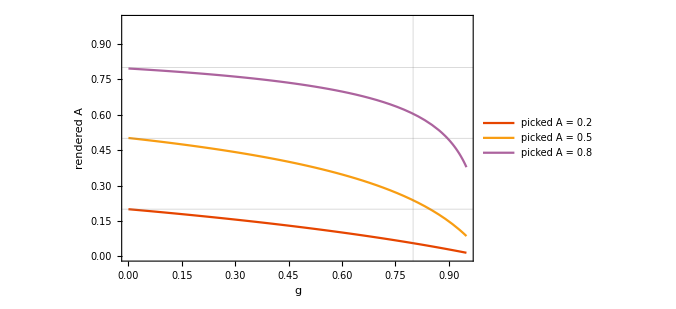

```mathematica
Plot[Evaluate[Table[AvdH[alphaChiang[A0], g], {A0, {0.2, 0.5, 0.8}}]], {g, 0, 0.95},
 PlotRange -> {0, 1}, Frame -> True, ImageSize -> 500,
 GridLines -> {{0.8}, {0.2, 0.5, 0.8}}, PlotTheme -> "WarmColor",
 PlotLegends -> {"picked A = 0.2", "picked A = 0.5", "picked A = 0.8"},
 FrameLabel -> {"g", "rendered A"}]
```

Where Pixar's fit runs out (mid gray, A = 0.5):

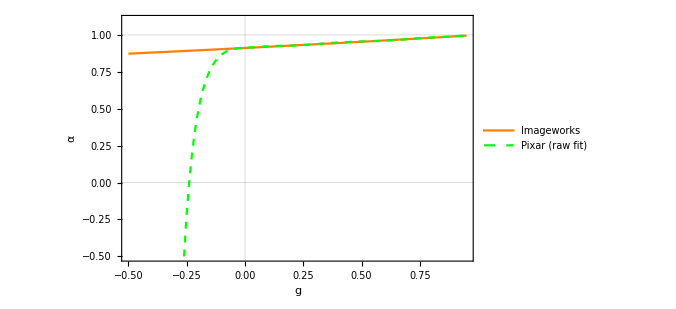

```mathematica
Plot[{alphaVdH[0.5, g], alphaPixarRaw[0.5, g]}, {g, -0.5, 0.95},
 PlotRange -> {-0.5, 1.1}, Frame -> True, ImageSize -> 500,
 PlotStyle -> {Directive[Thick, Orange], Directive[Thick, Dashed, Green]},
 PlotLegends -> {"Imageworks", "Pixar (raw fit)"},
 GridLines -> {{0}, {0, 1}}, FrameLabel -> {"g", "α"}]
```

Near white: mean bounces before absorption, 1/(1 − α), against a typical bounce limit of 256.

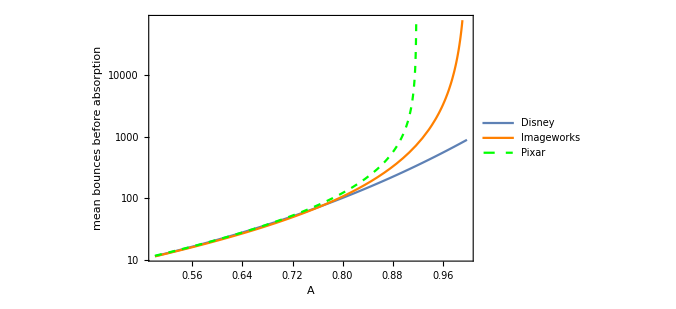

```mathematica
LogPlot[{1/(1 - alphaChiang[A]), 1/(1 - alphaVdH[A]), 1/(1 - alphaPixar[A, 0])}, {A, 0.5, 0.999},
 Frame -> True, ImageSize -> 500, GridLines -> {None, {256}},
 PlotStyle -> {Thick, Directive[Thick, Orange], Directive[Thick, Dashed, Green]},
 PlotLegends -> {"Disney", "Imageworks", "Pixar"},
 FrameLabel -> {"A", "mean bounces before absorption"}]
```

### Checks

```mathematica
clampFrom[g_] := First[Select[Range[0., 1., 0.001], alphaPixarRaw[#, g] >= 0.999999 &], None];

TableForm[{
  {"max |Imageworks - Disney| at g = 0", Max[Table[Abs[alphaVdH[A] - alphaChiang[A]], {A, 0, 1, 0.001}]]},
  {"A = 0.5, g = 0    Pixar | Imageworks", {alphaPixar[0.5, 0.], alphaVdH[0.5, 0.]}},
  {"A = 0.5, g = 0.8  Pixar | Imageworks", {alphaPixar[0.5, 0.8], alphaVdH[0.5, 0.8]}},
  {"A = 0.5, g = -0.3 Pixar raw fit", alphaPixarRaw[0.5, -0.3]},
  {"Pixar hits the clamp from A =  (g = 0 | 0.5 | 0.8)", clampFrom /@ {0., 0.5, 0.8}},
  {"Disney at A = 0.5, g = 0.8 renders A =", AvdH[alphaChiang[0.5], 0.8]}}]
```

max |Imageworks - Disney| at g = 0 | 0.00186524
A = 0.5, g = 0    Pixar | Imageworks | 0.913701
0.911709
A = 0.5, g = 0.8  Pixar | Imageworks | 0.982708
0.981
A = 0.5, g = -0.3 Pixar raw fit | -2.26642
Pixar hits the clamp from A =  (g = 0 | 0.5 | 0.8) | 0.919
0.857
0.791
Disney at A = 0.5, g = 0.8 renders A = | 0.237707

## 3. The radius

```mathematica
(* sigma_t per channel, per remap. col = {Ar, Ag, Ab}, r = radius, w = Framestore Rayleigh fraction.
   massaged = True: pipeline-style radius (r/4Pi, then /s(A) for all but Framestore). Adobe is never massaged. *)
burleyS[A_] := 1.9 - A + 3.5 (A - 0.8)^2;
rayleighR = {0.553, 0.808, 1.640};
remaps = {"Disney", "Imageworks", "Pixar", "Framestore", "Adobe"};

alphaOf[m_, A_, g_] := Switch[m,
   "Disney" | "Framestore", alphaChiang[A],
   "Imageworks" | "Adobe", alphaVdH[A, g],
   "Pixar", alphaPixar[A, g]];

sigmaT[m_, col_List, r_, g_, w_, massaged_] := Module[{al, d},
   al = alphaOf[m, #, g] & /@ col;
   d = Which[
     m === "Adobe" || ! massaged, ConstantArray[r, 3],
     m === "Framestore", ConstantArray[r/(4 Pi), 3],
     True, r/(4 Pi)/(burleyS /@ col)];
   Switch[m,
    "Disney", 1/(d (burleyS /@ col)),
    "Imageworks", 1/d,
    "Pixar", 1/(d (1 - g)),
    "Framestore", (rayleighR w + (1 - w))/(al d),
    "Adobe", With[{amax = Max[al]}, (1/r) amax/Max[#, amax 10^-3] & /@ al]]];

sigmaSA[m_, col_, r_, g_, w_, massaged_] := With[{st = sigmaT[m, col, r, g, w, massaged], al = alphaOf[m, #, g] & /@ col},
   {al st, st - al st}];   (* {sigma_s, sigma_a} *)
```

Same color, same radius: σt per channel for every remap. Tick the pipeline box to see what the 4π and s(A) massaging does.

```mathematica
Manipulate[
 BarChart[Table[sigmaT[m, {ar, ag, ab}, r, g, w, massaged], {m, remaps}],
  ChartLayout -> "Grouped", ChartStyle -> {Red, Green, Blue},
  ChartLabels -> {remaps, None}, ScalingFunctions -> "Log",
  Frame -> True, FrameLabel -> {None, "σt"}, ImageSize -> 600],
 {{massaged, True, "pipeline (4π, s(A))"}, {True, False}},
 {{r, 1., "radius"}, 0.1, 5., Appearance -> "Labeled"},
 {{g, 0., "g"}, 0., 0.95, Appearance -> "Labeled"},
 {{w, 0., "Framestore w"}, 0., 1., Appearance -> "Labeled"},
 Delimiter,
 {{ar, 0.8, "A red"}, 0.01, 0.99}, {{ag, 0.4, "A green"}, 0.01, 0.99}, {{ab, 0.2, "A blue"}, 0.01, 0.99}]
```

Matching radii to Disney's light reach (pipeline, g = 0): multiply by s(A) for Imageworks and Pixar, by s/α for Framestore.

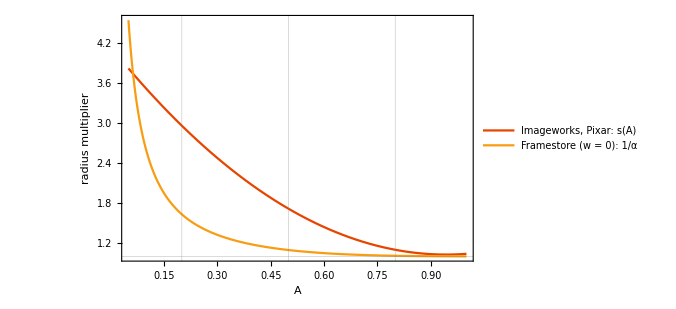

```mathematica
Plot[{burleyS[A], 1/alphaChiang[A]}, {A, 0.05, 1},
 Frame -> True, ImageSize -> 500, PlotTheme -> "WarmColor",
 GridLines -> {{0.2, 0.5, 0.8}, {1}},
 PlotLegends -> {"Imageworks, Pixar:  s(A)", "Framestore (w = 0):  1/α"},
 FrameLabel -> {"A", "radius multiplier"}]
```

Where the color lives: σs and σa per channel. Per-channel remaps spread color over both; Adobe keeps σs gray, Framestore tints it along the Mie–Rayleigh line. The swatch is the scattering color alone.

```mathematica
swatch[v_] := Graphics[{RGBColor @@ (v/Max[v]), Rectangle[]}, ImageSize -> 40];

Manipulate[
 Grid[Prepend[
   Table[With[{sa = sigmaSA[m, {ar, ag, ab}, 1., g, w, False]},
     {m,
      BarChart[sa, ChartLayout -> "Grouped", ChartStyle -> {Red, Green, Blue},
       ChartLabels -> {{"σs", "σa"}, None}, ImageSize -> 260, AspectRatio -> 0.5],
      swatch[sa[[1]]]}], {m, remaps}],
   {"", "radius 1, paper conventions", "σs color"}], Alignment -> {Left, Center}],
 {{g, 0., "g"}, 0., 0.95, Appearance -> "Labeled"},
 {{w, 0.64, "Framestore w"}, 0., 1., Appearance -> "Labeled"},
 Delimiter,
 {{ar, 0.8, "A red"}, 0.01, 0.99}, {{ag, 0.4, "A green"}, 0.01, 0.99}, {{ab, 0.2, "A blue"}, 0.01, 0.99}]
```

### Checks

```mathematica
(* the article's numbers: radius 1, g = 0, bright channel A = 0.8, dark channel A = 0.2 *)
probe = {0.8, 0.5, 0.2};
TableForm[
 Table[{m, sigmaT[m, probe, 1., 0., 0., True][[{1, 3}]]}, {m, Most[remaps]}],
 TableHeadings -> {None, {"pipeline σt", "{bright, dark}"}}]

(* Framestore skin example (paper conventions, w = 0.64, radius 1) *)
sigmaSA["Framestore", {0.8, 0.4, 0.2}, 1., 0., 0.64, False]

(* Adobe: sigma_s identical in every channel, whatever the color *)
Equal @@ Round[First[sigmaSA["Adobe", RandomReal[{0.05, 0.95}, 3], 1., 0.5, 0., False]], 10.^-10]
```

pipeline σt | {bright, dark}
Disney | 12.5664
12.5664
Imageworks | 13.823
37.1965
Pixar | 13.823
37.1965
Framestore | 12.6921
20.5056

{{0.71392,0.87712,1.4096},{0.00714377,0.154976,0.890563}}

True

## 4. Chromatic extinction: sampling distances

Three channels, three σt. Estimate the light scattered inside a slab of thickness d, the integral over [0, d] of σs e^(−σt t) dt, per channel, from one sampled distance. A: sample with red's σt. B: pick the channel by albedo (× throughput, here 1), then weight by all three channels' pdfs (one-sample MIS, balance heuristic).

```mathematica
(* Setup: sigma_t red = 1, blue = k, green in between; distances on [0, d] *)
albedo3 = {0.9, 0.8, 0.7};
sigmaTOf[k_] := {1., Sqrt[k], k};

sampleT[s_, d_] := -Log[1 - RandomReal[] (1 - Exp[-s d])]/s;            (* truncated exponential *)
pdfT[s_, d_, t_] := s Exp[-s t]/(1 - Exp[-s d]);                           (* listable over channels *)

fCh[st_, t_] := albedo3 st Exp[-st t];                                     (* sigma_s e^(-sigma_t t) *)
exactCh[st_, d_] := albedo3 (1 - Exp[-st d]);

estRed[st_, d_] := With[{t = sampleT[st[[1]], d]}, fCh[st, t]/pdfT[st[[1]], d, t]];

estMIS[st_, d_] := Module[{q = albedo3/Total[albedo3], j, t},
   j = RandomChoice[q -> {1, 2, 3}];
   t = sampleT[st[[j]], d];
   fCh[st, t]/Total[q pdfT[st, d, t]]];
```

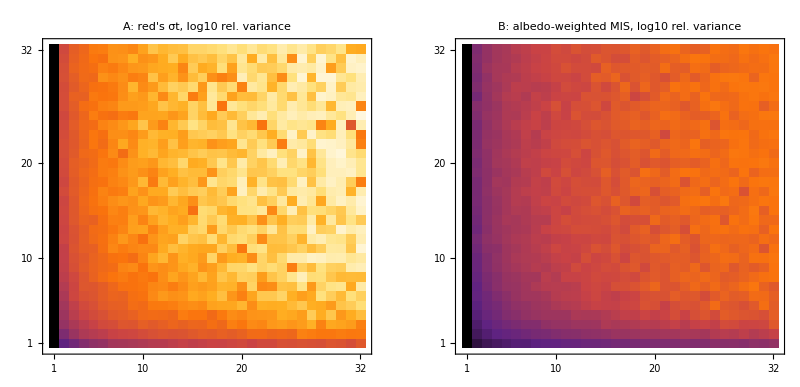

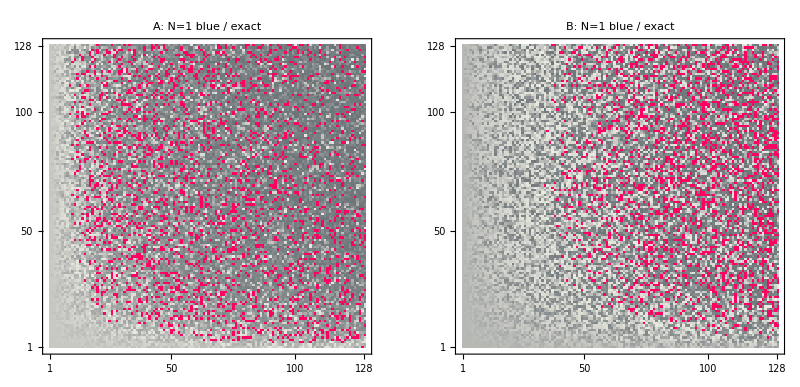

```mathematica
(* Monte Carlo Estimator Variance Benchmark *)
(* TOP: relative variance of the blue channel (log10, 64 trials per pixel) | BOTTOM: single-sample (N=1) blue estimate / exact *)
(* x: blue/red extinction ratio k in [1, 20], y: slab thickness d in [0.1, 5] mean free paths of red *)
(* first run launches the parallel kernels; SeedRandom does not reach them, so maps vary slightly run to run *)

nTrials = 64; res = 32; freq = 128;
kOf[i_, n_] := 1. + 19. (i - 1)/(n - 1);
dOf[i_, n_] := 0.1 + 4.9 (i - 1)/(n - 1);

relVar[est_, k_, d_] := With[{st = sigmaTOf[k]},
   Log10[Max[10^-6, Variance[Table[est[st, d][[3]], {nTrials}]]/exactCh[st, d][[3]]^2]]];   (* k = 1: all channels equal, zero variance *)

redVar = ParallelTable[relVar[estRed, kOf[x, res], dOf[y, res]], {y, res}, {x, res}];
misVar = ParallelTable[relVar[estMIS, kOf[x, res], dOf[y, res]], {y, res}, {x, res}];
range = MinMax[Flatten[{redVar, misVar}]];

redNoise = ParallelTable[With[{st = sigmaTOf[kOf[x, freq]], d = dOf[y, freq]},
    estRed[st, d][[3]]/exactCh[st, d][[3]]], {y, freq}, {x, freq}];
misNoise = ParallelTable[With[{st = sigmaTOf[kOf[x, freq]], d = dOf[y, freq]},
    estMIS[st, d][[3]]/exactCh[st, d][[3]]], {y, freq}, {x, freq}];

GraphicsGrid[{{
   MatrixPlot[redVar, ColorFunction -> "SunsetColors", PlotRange -> range, DataReversed -> True,
    PlotLabel -> "A: red's σt, log10 rel. variance"],
   MatrixPlot[misVar, ColorFunction -> "SunsetColors", PlotRange -> range, DataReversed -> True,
    PlotLabel -> "B: albedo-weighted MIS, log10 rel. variance"]}}, ImageSize -> 800]
GraphicsGrid[{{
   MatrixPlot[redNoise, PlotRange -> {0, 2}, ColorFunction -> "GrayTones", DataReversed -> True,
    PlotLabel -> "A: N=1 blue / exact"],
   MatrixPlot[misNoise, PlotRange -> {0, 2}, ColorFunction -> "GrayTones", DataReversed -> True,
    PlotLabel -> "B: N=1 blue / exact"]}}, ImageSize -> 800]
```

### Checks

```mathematica
(* both strategies are unbiased: means over many samples match the exact per-channel values *)
With[{st = sigmaTOf[10.], d = 2., n = 10^5},
 TableForm[{exactCh[st, d], Mean[Table[estRed[st, d], {n}]], Mean[Table[estMIS[st, d], {n}]]},
  TableHeadings -> {{"exact", "A: red's σt", "B: MIS"}, {"red", "green", "blue"}}]]
```

| red | green | blue
exact | 0.778198 | 0.798567 | 0.7
A: red's σt | 0.778198 | 0.797264 | 0.699612
B: MIS | 0.778251 | 0.797487 | 0.701021

## 5. A pinch of Rayleigh

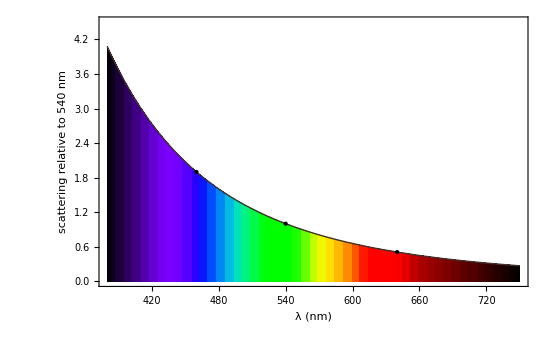

```mathematica
(* 1/lambda^4 across the visible range, normalized to green = 540 nm; Adobe's RGB wavelengths marked *)
lambdaRGB = {640., 540., 460.};
rayleigh[l_] := (540./l)^4;

Show[
 Plot[rayleigh[l], {l, 380, 750}, Frame -> True, ImageSize -> 550,
  ColorFunction -> (ColorData["VisibleSpectrum"][#1] &), ColorFunctionScaling -> False,
  Filling -> Axis, PlotStyle -> Thick, PlotRange -> {0, 4.5},
  FrameLabel -> {"λ (nm)", "scattering relative to 540 nm"}],
 ListPlot[Transpose[{lambdaRGB, rayleigh /@ lambdaRGB}],
  PlotStyle -> Directive[Black, PointSize[Large]]]]
```

Same 1/λ^4, two normalizations: Adobe pins green to 1, Framestore makes the three channels average to 1.

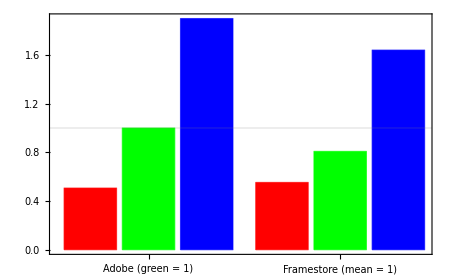

```mathematica
adobeScale = rayleigh /@ lambdaRGB;                  (* {~0.51, 1, ~1.90} *)
framestoreR = {0.553, 0.808, 1.640};                 (* mean 1 *)

BarChart[{adobeScale, framestoreR}, ChartLayout -> "Grouped", ChartStyle -> {Red, Green, Blue},
 ChartLabels -> {{"Adobe (green = 1)", "Framestore (mean = 1)"}, None},
 GridLines -> {None, {1}}, Frame -> True, ImageSize -> 450]
```

Slide them: Adobe scales red and blue extinction around green (negative values tint the other way), Framestore blends gray Mie scattering into Rayleigh. Swatches show the per-channel scattering emphasis.

```mathematica
swatchN[v_] := Graphics[{RGBColor @@ (v/Max[v]), Rectangle[]}, ImageSize -> 60];

Manipulate[
 With[{adobe = {1 + (adobeScale[[1]] - 1) t, 1., 1 + (adobeScale[[3]] - 1) t},
   frame = framestoreR w + (1 - w)},
  Grid[{
    {"Adobe extinction scale", BarChart[adobe, ChartStyle -> {Red, Green, Blue}, PlotRange -> {0, 3}, ImageSize -> 220],
     swatchN[adobe]},
    {"Framestore scattering s", BarChart[frame, ChartStyle -> {Red, Green, Blue}, PlotRange -> {0, 3}, ImageSize -> 220],
     swatchN[frame]}}, Alignment -> {Left, Center}]],
 {{t, 1., "Adobe rayleigh"}, -1., 1., Appearance -> "Labeled"},
 {{w, 0.64, "Framestore w"}, 0., 1., Appearance -> "Labeled"}]
```

### Checks

```mathematica
TableForm[{
  {"blue vs red scattering, 460 vs 640 nm", (640./460.)^4},
  {"Adobe red | blue extinction scale", adobeScale[[{1, 3}]]},
  {"Adobe red | blue mean free path at rayleigh = 1", 1/adobeScale[[{1, 3}]]},
  {"Framestore r mean", Mean[framestoreR]},
  {"implied lambda_red / lambda_blue   Adobe | Framestore", {640./460., (framestoreR[[3]]/framestoreR[[1]])^(1/4)}}}]
```

blue vs red scattering, 460 vs 640 nm | 3.74704
Adobe red | blue extinction scale | 0.506822
1.89908
Adobe red | blue mean free path at rayleigh = 1 | 1.97308
0.52657
Framestore r mean | 1.00033
implied lambda_red / lambda_blue   Adobe | Framestore | 1.3913
1.31229

## References

Chiang, M. J.-Y., Kutz, P., Burley, B. (2016). Practical and Controllable Subsurface Scattering for Production Path Tracing. ACM SIGGRAPH 2016 Talks.
Christensen, P. H., Burley, B. (2015). An Approximate Reflectance Profile for Efficient Subsurface Scattering. ACM SIGGRAPH 2015 Talks.
Henyey, L. G., Greenstein, J. L. (1941). Diffuse Radiation in the Galaxy. Astrophysical Journal 93, 70–83.
Jensen, H. W., Marschner, S. R., Levoy, M., Hanrahan, P. (2001). A Practical Model for Subsurface Light Transport. SIGGRAPH 2001.
Kulla, C., Conty, A. (2017). Revisiting Physically Based Shading at Imageworks. ACM SIGGRAPH 2017 Course: Physically Based Shading in Theory and Practice.
Kutz, P., et al. (2021). Novel Aspects of the Adobe Standard Material. Adobe technical report.
Masse, M. O., Walster, N. (2023). Artist Friendly Physically Plausible Attenuation. DigiPro 2023.
Novák, J., Georgiev, I., Hanika, J., Jarosz, W. (2018). Monte Carlo Methods for Volumetric Light Transport Simulation. Computer Graphics Forum 37(2).
van de Hulst, H. C. (1980). Multiple Light Scattering: Tables, Formulas, and Applications. Academic Press.
Wrenninge, M., Villemin, R., Hery, C. (2017). Path Traced Subsurface Scattering using Anisotropic Phase Functions and Non-Exponential Free Flights. Pixar Technical Memo 17-07.